```mathematica
Vaje iz Računalniška orodja v matematiki, 13. november 2018
```

```mathematica
Graphics3D[Hyperplane[{2, 2, 3}, {3, 5, 3}]]
```

-Graphics3D-

```mathematica
1. NALOGA
```

```mathematica
v0 = {10,3};
GG = 9.81;
H = 10;
a = {0,-GG};
x0 = {0, H};
```

```mathematica
v[t_] := v0 + a*t
X[t_] := x0 + v0*t + a*t^2/2
```

```mathematica
v0 + a*t
```

{10,3-9.81 t}

```mathematica
v[1]
```

{10,-6.81}

```mathematica
SlikaTocke[t_] := {PointSize[0.03],Point[X[t]]};
```

```mathematica
Graphics[SlikaTocke[1]]
```

-Graphics-

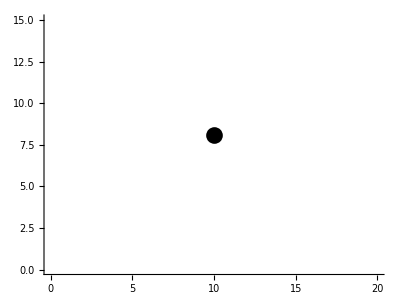

```mathematica
Graphics[SlikaTocke[1], Axes->True, PlotRange-> {{0,20}, {0, 15}}]
```

```mathematica
x0 + v0 + t + a*t^2/2
```

{10+t,13+t-4.905 t^2}

```mathematica
v[1]
v[2]
```

{10,-6.81}

```mathematica
{10,-16.62}
```

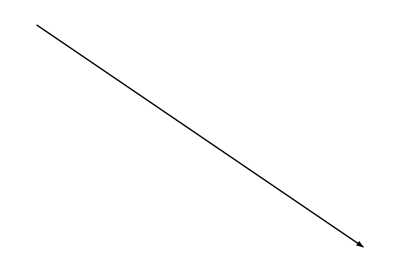

```mathematica
Graphics[Arrow[{{0,0}, v[1]}]]
```

```mathematica
SlikaVektorja[t_] := {Arrow[{{0,0}, v[t]}]}
SlikaVektorja2[t_] := {Arrowheads[i], Arrow[{{0,0}, v[t]}]}
Table[Graphics[SlikaVektorja2[1]], {i, {.05}}]
```

{-Graphics-}

```mathematica
Graphics[SlikaVektorja[1]]
```

-Graphics-

```mathematica
Manipulate[Graphics[SlikaTocke[t], Axes->True, PlotRange-> {{-1,25}, {-5, 15}}], {t, 0, 5}]
```

```mathematica
SlikaTocke[t_]:={PointSize[0.03],Point[X[t]]}
Manipulate[Graphics[SlikaTocke[t],Axes->True, PlotRange->{{0,20},{0,15}}, AspectRatio->Automatic], {t,0,3}]
```

```mathematica
X[t][[2]]==0
```

10+3 t-4.905 t^2==0

```mathematica
dolzinaHitrosti = (v0[[1]]^2+v0[[2]]^2)^(1/2)
sinkot =v0[[2]]/ dolzinaHitrosti //N
NajvišjeTočka = dolzinaHitrosti^2* sinkot^2 / (2*GG)+ H
```

√109

0.287348

10.4587

```mathematica
časLetaDonajvišjeTočke = 2*dolzinaHitrosti*sinkot/(GG *2)
domet  =dolzinaHitrosti^2 *Sin[2*ArcSin[sinkot]]/GG + H
```

0.30581

16.1162

```mathematica
časLeta= časLetaDonajvišjeTočke + (2*NajvišjeTočka/GG) ^(1/2)
```

1.76604

```mathematica
cas = v[časLeta]
```

{10.,-14.3248}

```mathematica
absHitrosti=((cas[[1]]) ^2 +  (cas[[1]]) ^2)^(1/2)
```

14.1421

```mathematica
2. NALOGA
```

```mathematica
r111 = Ravnina[{-1,-1,-1},{1,1,1}]
Slika[Ravnina[n_,v_]] := Hyperplane[n,v]
```

-Graphics3D-

```mathematica
Format[r_Ravnina] := Graphics3D[Slika[r]]
r111
```

-Graphics3D-

```mathematica
Normala[Ravnina[n_,v_]]:=n
```

```mathematica
Tocka[Ravnina[n_,v_]]:=v
```

```mathematica
rx=Ravnina[{1, 0, 0}, {0, 0, 0}];
SlikaNormale[Ravnina[n_, v_]] :=Arrow[{v, v + n}]
```

```mathematica
Graphics3D[{Slika[r111],SlikaNormale[r111]}]
```

-Graphics3D-

```mathematica
ravnine = {r111, rx};
obeSliki[r_Ravnina] := {Slika[r],SlikaNormale[r]}
Graphics3D[Map[obeSliki, ravnine]]
```

-Graphics3D-

```mathematica
Graphics3D[Map[{Slika[#],SlikaNormale[#]}&, ravnine]]
```

-Graphics3D-

```mathematica
rx=Ravnina[{1,0,0},{0,0,0}]
ry= Ravnina[{0,1,0},{0,0,0}]
rz= Ravnina[{0,0,1},{0,0,0}]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

```mathematica
SlikaNormale[Ravnina[n_, v_]] :=Arrow[{v, v + n}]
```

```mathematica
Graphics3D[SlikaNormale[r111]]
```

-Graphics3D-

```mathematica
Graphics3D[{Slika[rx],Slika[ry],Slika[rz],Slika[r111]}]
```

-Graphics3D-

```mathematica
ravnine //Map[obeSliki, #]& // Graphics3D[#]&
```

-Graphics3D-

```mathematica
ravnine = {rx, ry, rz, r111}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
SlikaNormale[Ravnina[n_, v_]] := Arrow[{v, v + n}]
slikeRavnin = Map[Slika, ravnine];
slikeNormal = Map[SlikaNormale, ravnine];
Graphics3D[{slikeRavnin, slikeNormal}, PlotRange->{{-1, 4}, {-1, 4},{-1, 4}}]
```

-Graphics3D-

```mathematica
SlikaTrikotnikov[{r1_, r2_, r3_, r4_}] := Map[Trikotnik[#, Presecisca[{r1, r2, r3, r4}]]&, {r1, r2, r3, r4}]
```

### 3. NALOGA

```mathematica
str1= {4,5,6}
str2 = {5,6,2}
str3 = {5,1,4}
str4 = {3,5,9}
```

{4,5,6}

{5,6,2}

{5,1,4}

{3,5,9}

```mathematica
tocke = {str1,str2,str3,str4}
```

{{4,5,6},{5,6,2},{5,1,4},{3,5,9}}

```mathematica
Graphics3D[Parallelepiped[str1,{str2,str3,str4}]]
```

-Graphics3D-